## Draft Computational Essay

#### Introduction

Multiway systems are systems generated by a set of rules that are recursively applied to all of the outputs.

#### Observations

Generally, with a linear or multiplicative multiway systems, merging behavior can be predicted by the various constant values.

Consider a system of the form

```mathematica
n |-> {an, n + b}
```

With this, we can predict the initial grid like pattern that arises, at least from the lower level branches.

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{5x,x+3}],{n},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{8}]]]]]
```

-Graphics-

where the left hand side will always have a+1 sides, and the right hand side has 2 sides, resulting in (a+3)-gons, as explained by Stephen Wolfram’s work “Multicomputation with Numbers: The Case of Simple Multiway Systems”. However, there are some exceptions to this behavior.  
For example, consider the rule set

```mathematica
n|->{2n, n+5}
```

The resulting graph ends up with one heptagon, with the remaining grids being pentagons. Every pentagon is also in the format of the generalized (n+3)-gon as explained above, which is trivial to see.

```mathematica
ResourceFunction["NestGraphTagged"][n↦{2n, n+5},{1},7,"StateLabeling"->True, PlotLegends->TraditionalForm/@{2n, n+5}]
```

-Graphics-

Zooming in on the heptagon subset, we see

```mathematica
Graph[With[{g=ResourceFunction["NestGraphTagged"][x|->Expand[{2x,x+5}],{1},6,"StateLabeling"->True]},Subgraph[g,First/@First[FindCycle[UndirectedGraph[g],{7}]]]]]
```

-Graphics-

Conveniently,

$Aborted

```mathematica
∃x∈Ζ^+ | a^x
```

and this can easily be seen as true, as an integer x would exist through Fermat’s Little Theorem, since a and b are relatively prime.

#### Dyck Paths

Dyck paths are lattice paths from (0, 0) to (n, n)that do not pass above the diagonal (y=x). For example, here’s an Dyck path where n=6.

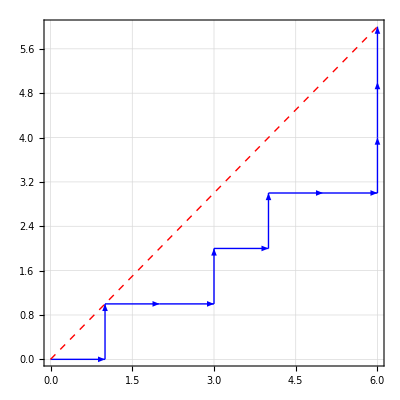

From any given point, a path can be generated by the map

```mathematica
{x, y} |-> {{x+1, y}, {x,y+1}}
```

or simply right and up “moves”. However, to make this path into a Dyck path, we will have to consider the restriction of the diagonal. To turn this into a multiway graph, I recursively build the graph by finding the next edge with the rule described above.

```mathematica
dyckNext[lst_List, n_Integer] := Module[{x := Last[lst][[2]][[1]], y := Last[lst][[2]][[2]]},
	Which[
		Length[lst] == 0, {{{0, 0}, {1, 0}}},
		x==n, {{{x, y}, {x, y + 1}}},
		x > y, {{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, 
		True,{{{x, y}, {x + 1, y}}}
	]
]
```

The which above hard codes the empty set case and the ending case (i.e., all up), and checks the ending lattice point of the last edge to consider how many of the paths would be valid.

```mathematica
dyckNext[{}, 6]
dyckNext[{{{0, 0}, {1, 0}}}, 6]
dyckNext[{{{0, 0}, {1, 0}}, {{1,0},{1,1}}}, 6]
```

{{{0,0},{1,0}}}

{{{1,0},{2,0}},{{1,0},{1,1}}}

{{{1,1},{2,1}}}

This function generates the Dyck path from the list of edges provided.

```mathematica
dyckGraph[lst_List, n_Integer] := Graphics[
	{Blue, Arrow[Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[{{0, 0}, {n, n}}]}, 
	Frame -> True,
	GridLines -> Automatic,
	ImageSize -> Full
]
```

We test this, as well as a function to generate random Dyck Paths below.

```mathematica
generateDyckPath[n_Integer] := Module[{lst = {}},
	Last[
		Table[
			AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*n]}
		]
	]
]
```

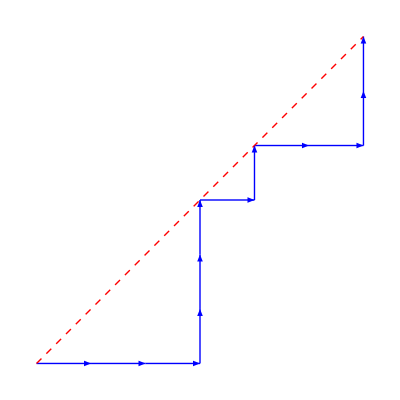

```mathematica
dyckGraph[generateDyckPath[6], 6]
```

In preparation of creating our multiway system, the display function will be updated to clear up some clutter.

```mathematica
dyckGraph[lst_List, n_Integer] := Graphics[
	{Blue, Arrow[Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[{{0, 0}, {n, n}}]}, 
	GridLines -> {Range[0, n, 1], Range[0, n, 1]},
	ImageSize -> 15
]
```

Now, to actually create the multiway system, we utilize the function “MultiwaySystem” from the Wolfram Research Repository.

```mathematica
showGraph[graphs_List, n_Integer, level_Integer] := ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n]],
	|>,
	{graphs}, level, "StatesGraph", 
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n], #1]&)
]
```

and we can call it below to generate a sample Dyck path multiway system.

```mathematica
n=4;
showGraph[{}, n, 2*n]
```

-Graphics-

Here’s an interactive you can play around with for both n and the level. It might be a bit lag inducing, so be warned.

```mathematica
Dynamic[n];
n=4;
Slider[Dynamic[n], {1, 10, 1}]
Dynamic[ListAnimate[Table[showGraph[{}, n, moves], {moves, Range[2 * n]}], AnimationRunning->False]]
```

Now, let’s take a look at the number of Dyck paths for each value of n.

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i], "Paths: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 1, 6, 1}]
]
```

-Graphics- | Paths: 1
-Graphics- | Paths: 2
-Graphics- | Paths: 5
-Graphics- | Paths: 14
-Graphics- | Paths: 42
-Graphics- | Paths: 132

Do the number of paths look familiar? To those well versed in number theory, you should recognize these as the Catalan numbers.

It is well known that the number of Dyck paths for a n×n-grid is equivalent to the n-th Catalan number. One visualization of the proof can be shown as such (proof rewritten from Stack Exchange).

Claim: The number of Dyck paths for a n×n-grid is equivalent to C_n, where

C_0=1, C_n=∑_(k=1)^n C_(k-1)C_(n-k)

Proof: Let the first time the path touches the diagonal be at (k, k), and we know that it must, as at the very least, the Dyck path will end at (n, n). Then, if we consider the first part (part in green), we can see that if we were to draw the line y=x-1, we would effectively get a Dyck path below on a k-1×k-1-grid, since it is the first time that it intersects with the line. On the other side, we would end up with an n-k×n-k-grid (highlighted in purple). As a result, by considering every possible value of k, from k=1 to k=n, we can split into the sum of two Catalan numbers C_k and C_(n-k), which gets us our desired summation above.

To get an interactive visualization, we need to create a few functions, as well as updating a few old ones (explanation later), in preparation for the next section.

Updated functions:

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Module[{x, y},
	x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
	y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
	Which[x==n, {{{x, y}, {x, y + 1}}}, 
	True, Select[{{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && !MemberQ[badEdges, #]&]]
]
generateDyckPath[n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] :=  Module[{lst = {}},
	Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n, resCol, badEdges]]], {i, Range[2*n]}]]
]
dyckGraph[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Graphics[{Blue, Arrow[
	Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[#] & /@ Table[{{i - 1, resCol[[i]]}, {i, resCol[[i + 1]]}}, {i, Range[n]}], Line[#] & /@ badEdges}, 
	GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->15
]
showGraph[graphs_List, level_Integer, resCol_List: Range[0, 10], badEdges_List:{}] :=ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n, resCol, badEdges]],
	"StateEquivalenceFunction"->SameQ,|>,
	{graphs},level,"StatesGraph",
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n, resCol, badEdges], #1]&)
]
```

New functions:

```mathematica
dyckGraphVis[lst_List, n_Integer, k_Integer] := Graphics[{Blue, Arrow[
	Partition[Flatten[lst, 1], 2]], 
	Purple, Arrow[Select[Partition[
		Flatten[lst, 1],2], #[[1]][[2]] >= k &] 
	], 
	Green, Arrow[Select[Partition[
		Flatten[lst, 1],2], k >=#[[2]][[1]] > 1&&#[[2]][[2]]<k&]
	],
	Red, Dashed, Line[{{0, 0}, {n, n}}], Line[{{1, 0}, {k, k - 1}}]}, 
	GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->Medium
]
genVisPath[n_Integer, k_Integer] := Module[{lst = generateDyckPath[k, Range[0, k], Table[{{i, i-1}, {i, i}}, {i, Range[k-1]}]]},
	If[n!=k, Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n]]], {i, Range[2*(n-k)]}]], lst]
]
```

Now for a visualization of the recursive proof for the case of n = 6 (and yes, there are degenerate cases for n - k and k, meaning one of them is equal to C_0)

```mathematica
n=6;
Dynamic[ListAnimate[Table[dyckGraphVis[genVisPath[n, k], n, k], {k, Range[n]}], AnimationRunning->False]]
```

There is a proof for the Catalan numbers iteratively involving generating functions, which will be explained briefly here as well.

#### Modifications

Now, we seek to explore modified Dyck graphs and analyze the changes in behavior and number of paths. For example, what happens when our restriction isn’t just a diagonal? What happens if we want to prevent paths from passing a specific edge? What would happen if we didn’t have to strictly travel right or up?

Once again, here is the list of updated functions.

```mathematica
dyckNext[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Module[{x, y},
	x = If[Length[lst] != 0, Last[lst][[2]][[1]], 0];
	y = If[Length[lst] != 0, Last[lst][[2]][[2]], 0];
	Which[x==n, {{{x, y}, {x, y + 1}}}, 
	True, Select[{{{x, y}, {x + 1, y}}, {{x, y}, {x, y + 1}}}, #[[2]][[2]]<=resCol[[#[[2]][[1]] + 1]] && !MemberQ[badEdges, #]&]]
]
generateDyckPath[n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] :=  Module[{lst = {}},
	Last[Table[AppendTo[lst, RandomChoice[dyckNext[lst, n, resCol, badEdges]]], {i, Range[2*n]}]]
]
dyckGraph[lst_List, n_Integer, resCol_List:Range[0, 10], badEdges_List : {}] := Graphics[{Blue, Arrow[
	Partition[Flatten[lst, 1], 2]], 
	Red, Dashed, Line[#] & /@ Table[{{i - 1, resCol[[i]]}, {i, resCol[[i + 1]]}}, {i, Range[n]}], Line[#] & /@ badEdges}, 
	GridLines->{Range[0,n, 1], Range[0,n, 1]}, ImageSize->15
]
showGraph[graphs_List, n_Integer, level_Integer, resCol_List: Range[0, 10], badEdges_List:{}] := ResourceFunction["MultiwaySystem"][
	<|"StateEvolutionFunction" -> Function[list, Append[list, #] & /@ dyckNext[list, n, resCol, badEdges]],
	"StateEquivalenceFunction"->SameQ,|>,
	{graphs}, level, "StatesGraph", 
	"StateRenderingFunction"->(Inset[dyckGraph[#2, n, resCol, badEdges],#1]&)
]
```

The functions above now have optional parameters resCol and badEdges, where resCol is the list of y-level restrictions by column (by default a range from 0 to n), and badEdges are a list of any specific edges that we want to ban.

For example, let’s prevent the Dyck paths from going through the edge (1, 0)--(2, 0). What happens then?

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{1, 0}, {2, 0}}}], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 2, 5, 1}]]
```

-Graphics- | Nodes: 1
-Graphics- | Nodes: 2
-Graphics- | Nodes: 5
-Graphics- | Nodes: 14

We end up with the (n-1)-th Catalan number, which is trivial to prove. All the resulting Dyck paths are forced to traverse from (0, 0) to (1, 0) to (1, 1), resulting in there being a Dyck path from (1, 1) to (n, n). This also implies blocking off (1, 0)--(1, 1) instead will result us in C_n-C_(n-1)paths instead.

What if we were to block off (2, 0)--(3, 0)?

```mathematica
Grid[Table[{graph = showGraph[{}, i,  2 * i, Range[0, i], {{{2, 0}, {3, 0}}}], "Nodes: " <> ToString[VertexCount[graph, _?(Last[#][[2]] == {i, i} &)]]}, {i, 3, 8, 1}]]
```

-Graphics- | Nodes: 4
-Graphics- | Nodes: 10
-Graphics- | Nodes: 28
-Graphics- | Nodes: 84
-Graphics- | Nodes: 264
-Graphics- | Nodes: 858